```mathematica
ClearAll["Global`*"]
```

```mathematica
(* NB: Units are GeV *)
MP = 938.27/1000;
MPI = 139.57/1000;
META = 547.8/1000;
METAP = 957.7/1000;

(*
Needs["PlotLegends`"]
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
*)

SetOptions[
{Plot, LogPlot, LogLogPlot,ErrorListLogPlot,ErrorListPlot,ErrorListLogLogPlot, ListPlot,ListLinePlot },{}];
```

```mathematica
(*Print["The path is:"]
path = "/Users/vincent/Dropbox/Arkaitz/param/"
SetDirectory[path];

(*load the plots *)
<<"plots.mx"*)

abs={0.76,0.8,0.84,0.88,0.9199999999999999,0.96,1.,1.04,1.08,1.12,1.16,1.2,1.24,1.28,1.3199999999999998,1.3599999999999999,1.4,1.44,1.48,1.52,1.56,1.6,1.6400000000000001,1.6800000000000002,1.72,1.76,1.8,1.84,1.8800000000000001,1.92,1.96,2.,2.04,2.08,2.12,2.16,2.2,2.24,2.2800000000000002,2.3200000000000003,2.3600000000000003,2.4000000000000004,2.44,2.48,2.52,2.56,2.6,2.64,2.6799999999999997,2.7199999999999998,2.76,2.8,2.84,2.88,2.92,2.96};
```

## Parametrization - P&D waves

```mathematica
t2=-0.1;
Λ = 1;
s01 = (MPI+META)^2;sm1 = (MPI-META)^2;
s02 = (MPI+METAP)^2;sm2 = (MPI-METAP)^2;
lam[a_,b_,c_]:= a^2+b^2+c^2-2(a b+ b c+ c a);
mom1[s_]:= Sqrt[(s-(META+MPI)^2)(s-(META-MPI)^2)]/Sqrt[4 s];
mom2[s_]:= Sqrt[(s-(METAP+MPI)^2)(s-(METAP-MPI)^2)]/Sqrt[4 s];
momQ[s_]:=Sqrt[s^2+t2^2+MPI^4-2(s t2+ t2 MPI^2 + MPI^2 s)]/Sqrt[4s];

numCM1[L_,s_]:=(Sqrt[(s-(META+MPI)^2)(s-(META-MPI)^2)])^(2L+1) /(s+Λ)^(2L+3);
numCM2[L_,s_]:= (Sqrt[(s-(METAP+MPI)^2)(s-(METAP-MPI)^2)])^(2L+1) /(s+Λ)^(2L+3);

(* Iρ = cm *)
cm1[L_,s_]:=I numCM1[L,s] HeavisideTheta[s-s01 ]+  s/π NIntegrate[numCM1[L,sp] /(sp-s)/sp  ,{sp,s01,∞},Method->"PrincipalValue",Exclusions->s-sp==0]//Quiet
cm2[L_,s_]:=I numCM2[L,s]HeavisideTheta[s-s02 ]  +  s/π NIntegrate[numCM2[L,sp] /(sp-s)/sp  ,{sp,s02,∞},Method->"PrincipalValue",Exclusions->s-sp==0]//Quiet
```

```mathematica
Clear[KP11, KP12, KP22, KD11, KD12, KD22, detKP, detKD, TinvP, TinvD, TmatP,TmatP,numP1,numP2,numD1,numD2,AP1,AP2,AD1,AD2]

ai = {
{408.74575, -632.5741,281.4765, -57.9772},   (*eta pi P wave*)
{-47.05312,65.836784,-20.962106,1.200548},(*etap pi P wave*)
{-247.8013,413.913500, -190.94051, 59.24574}, (*eta pi D wave*)
{230.92070, -290.65641, 176.88424, -3.822988}};  (*etap pi D wave*)

gi ={{-0.683129,-13.11520, 3.521284},
{ 5.62702664 ,-3.772147,1.857831},
{147.794305, -33.388853,8.056212}};

ci = {
{-15.434402,-67.2219,-190.733219},
{ -2402.56336, 462.6032325,-86.60076}};
di =  {
{1.817979, 7.6440647,63.854279},
{ -614.580173,164.72158,-42.18664}};

KP11[s_]:= gi[[1,1]]gi[[1,1]]/(gi[[1,3]]-s) + ci [[1,1]] + di [[1,1]]*s ;
KP12[s_]:= gi[[1,1]]gi[[1,2]]/(gi[[1,3]]-s)  + ci [[1,2]]+ di [[1,2]] *s;
KP22[s_]:= gi[[1,2]]gi[[1,2]]/(gi[[1,3]]-s) + ci [[1,3]] + di [[1,3]] *s;

KD11[s_]:= gi[[2,1]]gi[[2,1]]/(gi[[2,3]]-s)+ gi[[3,1]]gi[[3,1]]/(gi[[3,3]]-s) + ci [[2,1]]+ di [[2,1]]*s  ;
KD12[s_]:= gi[[2,1]]gi[[2,2]]/(gi[[2,3]]-s) + gi[[3,1]]gi[[3,2]]/(gi[[3,3]]-s) + ci [[2,2]]+ di [[2,2]]*s ;
KD22[s_]:= gi[[2,2]]gi[[2,2]]/(gi[[2,3]]-s)+ gi[[3,2]]gi[[3,2]]/(gi[[3,3]]-s) + ci [[2,3]]+ di [[2,3]]*s  ;

detKP[s_]:= KP11[s]KP22[s]-KP12[s]^2;
detKD[s_]:= KD11[s]KD22[s]-KD12[s]^2;

(* the inverse of T *)

TinvP[s_]:= 1/detKP[s]{{KP22[s], -KP12[s]},{-KP12[s], KP11[s]}} - {{cm1[1,s], 0}, {0, cm2[1,s]}}; 
TinvD[s_]:= 1/detKD[s]{{KD22[s], -KD12[s]},{-KD12[s], KD11[s]}} - {{cm1[2,s], 0}, {0, cm2[2,s]}}; 

TmatP[s_] := Inverse[TinvP[s]];
TmatD[s_] := Inverse[TinvD[s]];

unit = {{1,0},{0,1}};
tmpP[s_]:= unit- {{cm1[1,s], 0}, {0, cm2[1,s]}}. {{KP11[s], KP12[s]},{KP12[s], KP22[s]}};
tmpD[s_]:= unit- {{cm1[2,s], 0}, {0, cm2[2,s]}}. {{KP11[s], KP12[s]},{KP12[s], KP22[s]}};

TmatPb[s_] :=  {{KP11[s], KP12[s]},{KP12[s], KP22[s]}}.Inverse[tmpP[s]];
TmatDb[s_] :=  {{KD11[s], KD12[s]},{KD12[s], KD22[s]}}.Inverse[tmpD[s]];



numP1[s_]:= Sum[ai[[1,i]]ChebyshevT[i-1,s/(s+1)],{i,4}];
numP2[s_]:= Sum[ai[[2,i]]ChebyshevT[i-1,s/(s+1)],{i,4}];
numD1[s_]:= Sum[ai[[3,i]]ChebyshevT[i-1,s/(s+1)],{i,4}];
numD2[s_]:= Sum[ai[[4,i]]ChebyshevT[i-1,s/(s+1)],{i,4}];

AP1[s_]:= mom1[s]^(3/2)( numP1[s] TmatP[s][[1,1]] +numP2[s] TmatP[s][[1,2]] );
AP2[s_]:= mom2[s]^(3/2) ( numP1[s] TmatP[s][[2,1]] +numP2[s] TmatP[s][[2,2]] );

AD1[s_]:= mom1[s]^(3/2)( mom1[s]momQ[s])^1  ( numD1[s] TmatD[s][[1,1]] +numD2[s] TmatD[s][[1,2]]  );
AD2[s_]:= mom2[s]^(3/2)( mom2[s]momQ[s])^1 (  numD1[s] TmatD[s][[1,2]] + numD2[s] TmatD[s][[2,2]]);
```

```mathematica
ampP1= Table[AP1[abs[[i]]^2],{i,Length[abs]}];
ampP2= Table[AP2[abs[[i]]^2],{i,Length[abs]}];
ampD1= Table[AD1[abs[[i]]^2],{i,Length[abs]}];
ampD2= Table[AD2[abs[[i]]^2],{i,Length[abs]}];
```

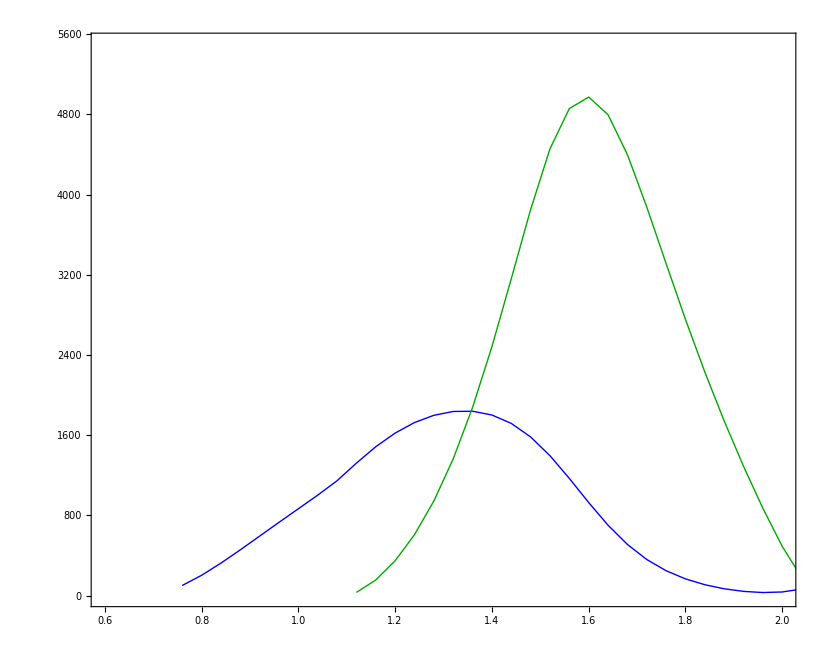

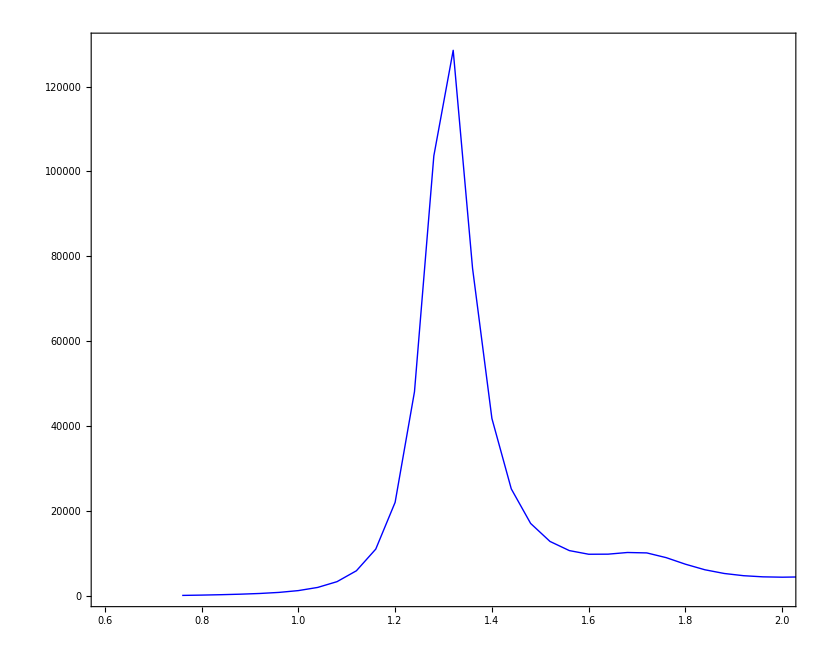

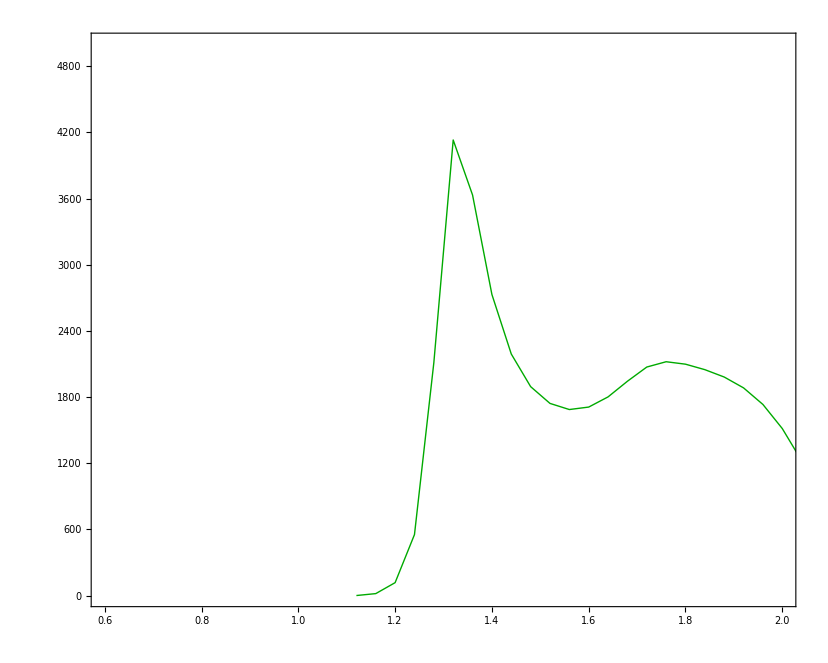

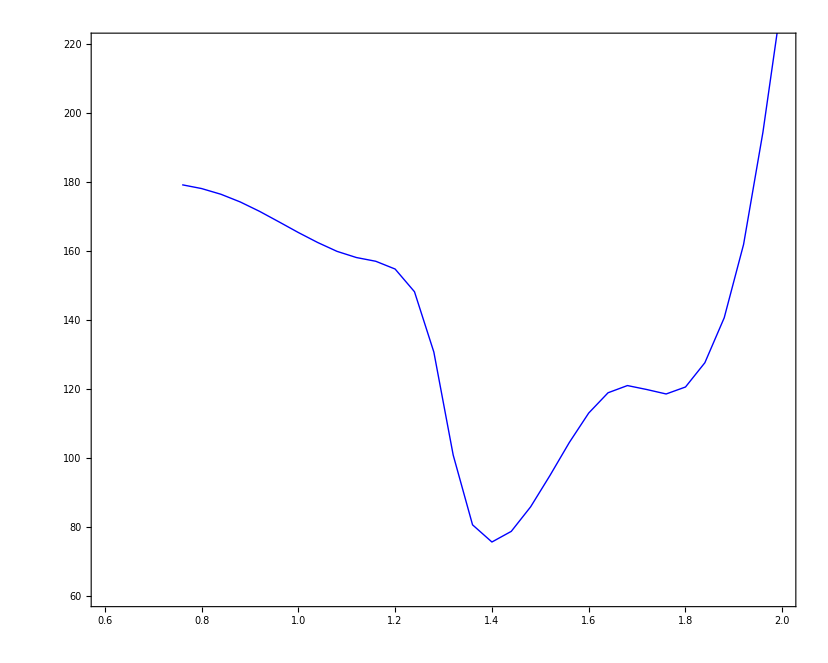

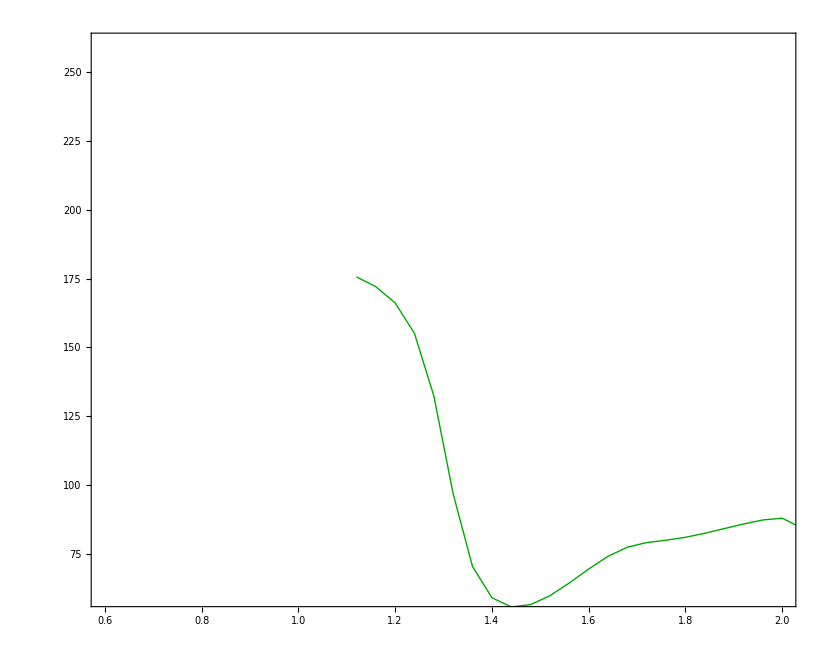

```mathematica
tabIP1 = Table[{abs[[i]],Abs[ampP1[[i]]]^2 },{i,Length[abs]}];
pIP1=ListLinePlot[tabIP1 , PlotStyle->{Blue, Thick}, PlotRange->All];

tabIP2 = Table[{abs[[i]],Abs[ampP2[[i]]]^2 },{i,10,Length[abs]}];
pIP2=ListLinePlot[tabIP2 , PlotStyle->{Darker@Green, Thick}, PlotRange->All];

tabID1 = Table[{abs[[i]],Abs[ampD1[[i]]]^2 },{i,Length[abs]}];
pID1=ListLinePlot[tabID1 , PlotStyle->{Blue, Thick}, PlotRange->All];

tabID2 = Table[{abs[[i]],Abs[ampD2[[i]]]^2 },{i,10,Length[abs]}];
pID2=ListLinePlot[tabID2, PlotStyle->{Darker@Green, Thick}, PlotRange->All];

p1=Show[pIP1,pIP2, PlotRange->{{0.6,2},{0,5500}}]
p2=Show[pID1, PlotRange->{{0.6,2},{0,130000}}]
p3=Show[pID2, PlotRange->{{0.6,2},{0,5000}}]


tmp=Arg[ampP1]-Arg[ampD1];
arg = Table[If[tmp[[i]]>0, tmp[[i]], tmp[[i]]+2π],{i,Length[abs]}];
tabϕP1 = Table[{abs[[i]],180/π arg[[i]] },{i,Length[abs]}];
pϕP1=ListLinePlot[tabϕP1 ,PlotStyle->{Blue, Thick}, PlotRange->All];

tabϕP2 = Table[{abs[[i]],180/π (Arg[ampP2[[i]]]-Arg[ampD2[[i]]] )+360*HeavisideTheta[-(Arg[ampP2[[i]]]-Arg[ampD2[[i]]])]},{i,10,Length[abs]}];
pϕP2=ListLinePlot[tabϕP2 , PlotStyle->{Darker@Green, Thick}, PlotRange->All];

Show[pϕP1, PlotRange->{{0.6,2},{60,220}}] 
Show[pϕP2, PlotRange->{{0.6,2},{60,260}}]
```